Define the distributions

```mathematica
kappaDist1D=n0(π (κ - 1/2) vth^2)^(-1/2)Gamma[κ+1]/Gamma[κ+1/2](1+v^2/((κ-1/2)vth^2))^(-(κ+1));
```

```mathematica
maxwellDist1D=n0(π vth^2)^(-1/2)Exp[-v^2/vth^2];
```

```mathematica
kappaDist3D=n0(π (κ - 3/2) vth^2)^(-3/2)Gamma[κ+1]/Gamma[κ-1/2](1+v^2/((κ-3/2)vth^2))^(-(κ+1));
```

```mathematica
maxwellDist3D=n0(π vth^2)^(-3/2)Exp[-v^2/vth^2];
```

Define thermal velocity (in km/s) as function of temperature (in eV)

```mathematica
uToeV = 931493614.838475;
c=299792.458; (*km/s*)
```

```mathematica
mOxy=15.999 * uToeV/c^2; (*eV/ (km/s) *)
```

```mathematica
mH=1.00794* uToeV/c^2;
```

```mathematica
mOxy
mH
```

0.165818

0.0104466

```mathematica
vthOx[T_]:=2*T/mOxy (*in km/s*)
```

```mathematica
vthH[T_]:=2*T/mH (*in km/s*)
```

Mas

```mathematica
T=1;
```

```mathematica
m3DOxy = maxwellDist3D/.{vth->vthOx[T],n0->1}
m3DH = maxwellDist3D/.{vth->vthH[T],n0->1}
```

0.000102348 ⅇ^(-0.00687389 v^2)

2.5592×10^-8 ⅇ^(-0.0000272826 v^2)

```mathematica
plotFuncs={m3DOxy,m3DH}
```

{0.000102348 ⅇ^(-0.00687389 v^2),2.5592×10^-8 ⅇ^(-0.0000272826 v^2)}

Integrals

#### Zeroth moment of the kappa dist and Maxwellian dist, just to see

```mathematica
Integrate[kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

n0

```mathematica
Integrate[maxwellDist,{v,-∞,∞},Assumptions->vth>0]
```

n0

#### Second moment of the kappa distribution

```mathematica
Integrate[v^2 kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

(n0 vth^2)/2

#### Now try the Baumjohann & Treumann integral (Equation (10.31), maybe?) This isn’t exact, but for example …

```mathematica
Integrate[(1-2ⅈ v-3 v^2)kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

n0-(3 n0 vth^2)/2

Plot the distributions (specify kappa vals to plot with plotKappaVals list)

See journal__20180419__1DKappadist.nb for original

#### Define functions to plot using units such that vth = 1 and n0 = 1

```mathematica
plotFuncs=(((kappaDist/.{κ->#})&/@plotKappaVals)~Join~{maxwellDist})/.{vth->1,n0->1}
```

{1.67566/((1+10. v^2)^1.6),1.06899/((1+3.33333 v^2)^1.8),0.758623/((1+1.05263 v^2)^2.45),(256 √2)/(189 π (1+(2 v^2)/9)^6),(ⅇ^(-v^2))/(√π)}

#### Define plot labels

```mathematica
plotLabelStrings={"Oxygen","Hydrogen"};
```

```mathematica
plotLabels=Style[#,Bold,FontSize->16]&/@plotLabelStrings;
```

#### Linear plot

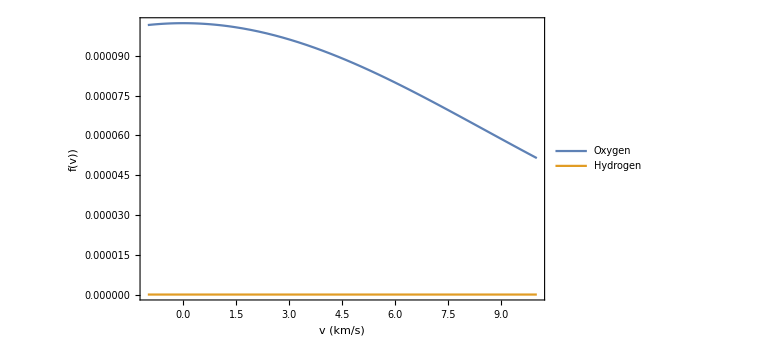

```mathematica
Plot[plotFuncs,{v,-1,10},PlotRange->Full,
PlotLegends->plotLabels,
Frame->True,FrameLabel->{"v (km/s)","f(v))"},FrameStyle->Directive[FontSize->16,Black,Bold],
ImageSize->Large]
```

#### Log-log plot to show the power-law tails that characterize kappa distributions

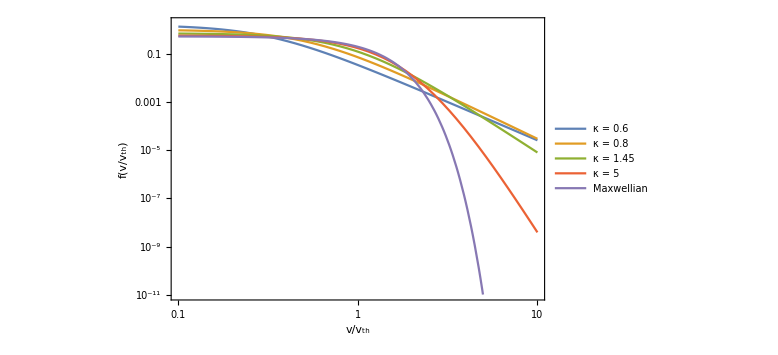

```mathematica
LogLogPlot[plotFuncs,{v,0.1,10},PlotRange->{{0.1,10},{10^-11,2}},
(*PlotLabels->Placed[(StringForm["κ = `1`",#]&/@plotKappaVals),Top],*)
PlotLegends->plotLabels,
Frame->True,FrameLabel->{"v/v_th","f(v/v_th)"},FrameStyle->Directive[FontSize->16,Black,Bold],
ImageSize->Large]
```